# VYA - Přednášky

## 3. Přednáška

### Používání AI

https://chat.openai.com/

Zadání: “Prosím, napiš skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos, sinus modře a kosínus červeně, popíše osy a graf bude mít GridLines”

Odpoveď: “Samozřejmě, zde je skript ve Wolfram Mathematica, který vygeneruje graf funkcí Sin a Cos s popisem os a s GridLines:”

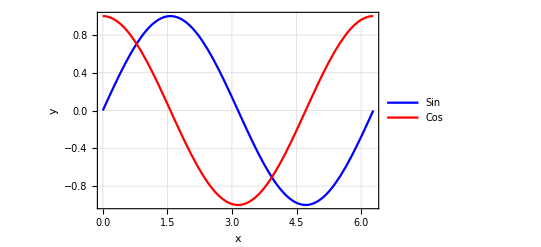

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{Style["x",Bold,14],Style["y",Bold,14]},PlotLegends->{"Sin","Cos"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400]
```

“Tento skript vykreslí graf funkcí Sin a Cos na intervalu [0, 2 Pi]. Sinus je vykreslen modře a kosinus červeně. Osa x je popsaná nápisem “x” a osa y nápisem “y”. Graf má také mřížky (GridLines) s šedým stylem (GridLinesStyle). Celková velikost grafu je nastavena na 400 pixelů.

Můžete tento skript spustit ve Wolfram Mathematica a zobrazí se vám výsledný graf.”

### Příkaz module

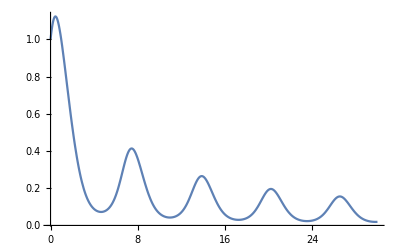

```mathematica
Quiet@Remove["Global`*"];
s[a_] := NDSolve[{y'[x] == y[x] Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}]
g[a_] := Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]
g[1]
```

```mathematica
Quiet@Remove["Global`*"];
f[a_] := Module[{reseni}, reseni = NDSolve[{y'[x] == y[x]Cos[x + a*y[x]], y[0] == 1}, y, {x, 0, 30}];
	Plot[Evaluate[y[x] /. s[a]], {x, 0, 30}, PlotRange -> All]]
f[2]
```

1

### Užitečná funkce Tanh

5/2+1/2 Tanh[5 (-4+x)]

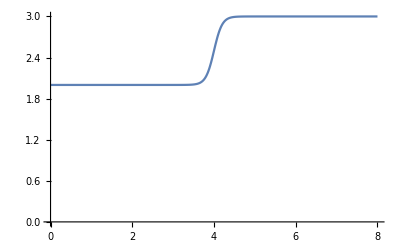

```mathematica
Quiet@Remove["Global`*"];
Prechod[Odkud_, Kam_, Zmena_, Strmost_, Promenna_] := Module[{Rovnice, a, b, Dosaz}, 
Rovnice = {a - b == Odkud, a + b == Kam};
Dosaz = Solve[Rovnice, {a, b}][[1]]; 
a+b*Tanh[Strmost*(Promenna - Zmena)] /. Dosaz];
Graf = Prechod[2, 3, 4, 5, x]
Plot[Graf, {x, 0, 8}, AxesOrigin -> {0, 0}]
```

### Pure functions

```mathematica
Quiet@Remove["Global`*"];
f[x_] := x^2;
f[5]
```

25

```mathematica
?#
```

```mathematica
#^2 & [5]
```

25

```mathematica
g[x_,y_] := x + y^2
g[E, Pi]
```

ⅇ+π^2

```mathematica
#1 + #2^2 & [E, Pi]
```

ⅇ+π^2

```mathematica
h := #1 + #2^2&
h[E, Pi]
```

ⅇ+π^2

```mathematica
?Select
```

```mathematica
Test[x_] := x > 2
Test[1]
Test[3]
Select[{1, 2, 4, 3, 7, 6, 5, 8}, Test]
```

False

True

{4,3,7,6,5,8}

```mathematica
Select[{1, 2, 4, 3, 7, 6, 5, 8}, # > 2 &]
```

{4,3,7,6,5,8}

```mathematica
# > 2 & [1]
```

False

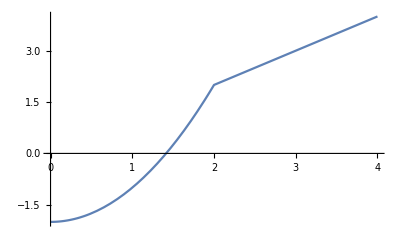

```mathematica
Quiet@Remove["Global`*"];
Test[x_] := x > 2
f[x_?Test] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

```mathematica
Quiet@Remove["Global`*"];
```

```mathematica
f[x_? (# > 2 &)] := x
f[x_] := x^2-2
Plot[f[x], {x, 0, 4}]
```

-Graphics-

### Map a Apply

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
?Map
```

```mathematica
Map[f, {1, 2, 3, 4}]
f /@ {1, 2, 3, 4}
```

{f[1],f[2],f[3],f[4]}

{f[1],f[2],f[3],f[4]}

```mathematica
Sin[{1, 2, 3, 4}]
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Sin /@ {1, 2, 3, 4}
```

{Sin[1],Sin[2],Sin[3],Sin[4]}

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Quiet[Remove["Global`*"]];
?Apply
```

```mathematica
Apply[f, {1, 2, 3, 4}]
f @@ {1, 2, 3, 4}
```

f[1,2,3,4]

f[1,2,3,4]

```mathematica
Apply[f, Map[f, {1, 2, 3, 4}]]
f @@ (f /@ {1, 2, 3, 4})
```

f[f[1],f[2],f[3],f[4]]

f[f[1],f[2],f[3],f[4]]

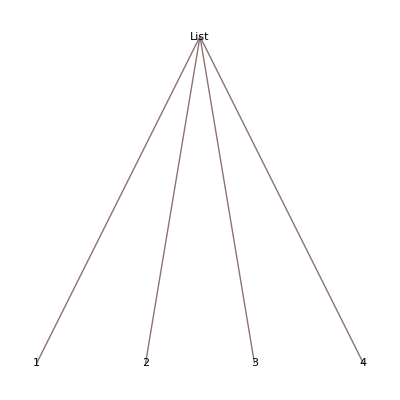
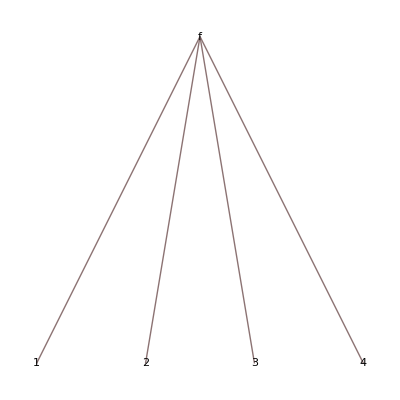

```mathematica
{TreeForm[{1, 2, 3, 4}], TreeForm[f @@ {1, 2, 3, 4}]}
```

{{-1,0,2},{5,2,0},{5,-5,0}}

(-1 | 0 | 2
5 | 2 | 0
5 | -5 | 0)

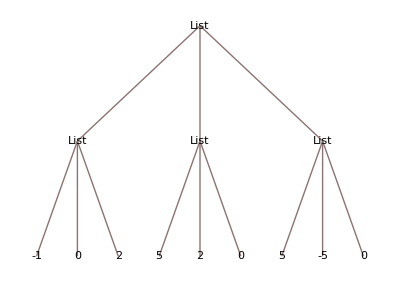

```mathematica
Matice = Table[RandomInteger[{-5,5}], {i,3}, {j,3}]
MatrixForm[Matice]
TreeForm[Matice]
```

```mathematica
Matice /. List -> Plus
```

8

```mathematica
f @@ Matice
Plus @@ Matice
```

f[{-1,0,2},{5,2,0},{5,-5,0}]

{9,-3,2}

```mathematica
f[x_] := x^3
f[Range[10]]
#^3 & /@ Range[10]
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
{1,8,27,64,125,216,343,512,729,1000}
```

```mathematica
Plus @@ (#^3 & /@ Range[10])
```

```mathematica
Plus @@ (#^3 & /@ Range[10])
∑_(i=1)^10 i^3
```

3025

3025


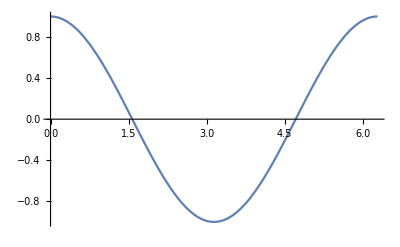
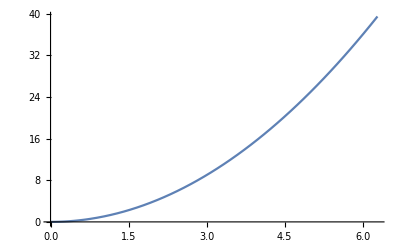

```mathematica
Plot[#[x], {x, 0, 2Pi}] & /@ {Sin, Cos, #^2 &}
```

### NumberQ a NumericQ

```mathematica
?NumberQ
```

```mathematica
?NumericQ
```

```mathematica
NumberQ[Pi]
```

False

```mathematica
NumericQ[Pi]
```

True

```mathematica
?N
```

```mathematica
Pi + 2E
```

2 ⅇ+π

```mathematica
N[Pi + 2E]
```

8.57816d

```mathematica
N[Pi, #] & /@ Range[5, 20, 1]
```

{3.1416,3.14159,3.141593,3.1415927,3.14159265,3.141592654,3.1415926536,3.14159265359,3.14159265359,3.1415926535898,3.14159265358979,3.141592653589793,3.1415926535897932,3.14159265358979324,3.141592653589793238,3.1415926535897932385}

### Eulerova metoda

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Derivace[{t_, y_}] := -2y;
PocBod = {t0, y0} = {0, 10};
tMax = 2;
nKroku = 10;
Δt = (tMax - t0)/nKroku
KrokEuler[Bod:{t_, y_}] := {t + Δt, y + Δt * Derivace[Bod]}
KrokEuler[PocBod]
```

1/5

{1/5,6}